# Differential

## Function

```mathematica
f[x_]=√x;
```

Point

```mathematica
Subscript[x, 1]=4;
```

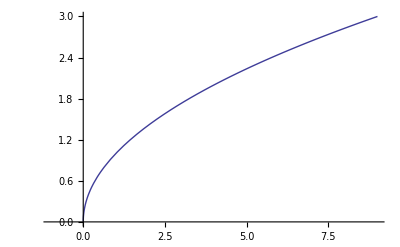

```mathematica
Plot[f[x],{x,Subscript[x, 1]-5,Subscript[x, 1]+5}]
```

```mathematica
table=Table[{Δx,Subscript[x, 1]+Δx,f[Subscript[x, 1]+Δx]-f[Subscript[x, 1]],f[Subscript[x, 1]+Δx],f'[Subscript[x, 1]]Δx,f[Subscript[x, 1]]+f'[Subscript[x, 1]]Δx},{Δx,{1,0.9,0.8,0.7,0.6,0.5,0.01,0.001}}];
```

```mathematica
head={"Δx","x_1+Δx","Δy=f[x_1+Δx]-f[x_1]","y+Δy","dy≃f'[x_1]Δx","y+dy"};
```

```mathematica
Grid[Insert[N[table],head,1],
ItemStyle->{Automatic,{1->{Bold,14}}},
Frame->{All,1->True},
Background->{None,{{LightBlue,LightRed}}}]
```

Δx | x_1+Δx | Δy=f[x_1+Δx]-f[x_1] | y+Δy | dy≃f'[x_1]Δx | y+dy
1. | 5. | 0.236068 | 2.23607 | 0.25 | 2.25
0.9 | 4.9 | 0.213594 | 2.21359 | 0.225 | 2.225
0.8 | 4.8 | 0.19089 | 2.19089 | 0.2 | 2.2
0.7 | 4.7 | 0.167948 | 2.16795 | 0.175 | 2.175
0.6 | 4.6 | 0.144761 | 2.14476 | 0.15 | 2.15
0.5 | 4.5 | 0.12132 | 2.12132 | 0.125 | 2.125
0.01 | 4.01 | 0.00249844 | 2.0025 | 0.0025 | 2.0025
0.001 | 4.001 | 0.000249984 | 2.00025 | 0.00025 | 2.00025